# Duffing System

The general 2nd order ODE is

```mathematica
{δ,β,α,ω}={0.02,-1,5, 0.5};
TMax=123456;
θ0=4.99;
{ySol,pPoints}=Reap[
NDSolveValue[{
θ'[t]==ω,
y''[t]+δ y'[t]+β y[t] + α y[t]^3== Cos[θ[t]],y[0]==0.452, y'[0]==1.776,θ[0]==θ0},
y,{t, 0, TMax},
Method->{"EventLocator","Event"->Mod[θ[t],2π] ==0.2,"Direction"->1, "EventAction":>Sow[{y[t],y'[t]}]}]];
```

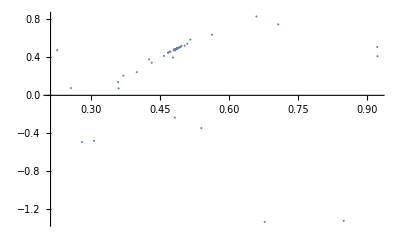

```mathematica
ListPlot[pPoints⟦1,30;;-1⟧,
PlotRange->All]
```